Illustrate three variables that sum to 100 % in a triangle 
where coordinates are {x, y} and “third dimension” y2:= 100 - x - y is depicted with gridlines and labels.

This triangle is also known as a “probability triangle”, used to depict mixed strategies in a game with three actions (e.g. “Rock, paper, scissors”)

Example data from WorldBank, using handpicked API calls here: 
https://data.worldbank.org/indicator/SP.POP.65UP.TO
Data fetched on 2023-01-06.

### Initialize

#### Paths

```mathematica
mainDir=SetDirectory[NotebookDirectory[]]
csvDir=FileNameJoin[{mainDir,"csv"}]
outputDir=FileNameJoin[{mainDir,"graphs"}]
```

#### Functions for probability triangle graphs

```mathematica
<<"sharesTriangle.wl"
```

### Import data tables, make series

```mathematica
csvPaths=FileNames[csvDir<>"/*"];
csvTabs=Import[#,"Data"]&/@csvPaths;
csvVarNames=FileBaseName/@csvPaths
Dimensions@csvTabs
```

{Population_ages_0-14_total,Population_ages_15-64_total,Population_ages_65_and_above_total,Population_total}

{4,63,6}

```mathematica
{pop14,pop1564,pop65,pop}=Take[#,{2,-1},{2,-1}]&/@csvTabs;
Dimensions@%
```

{4,62,5}

```mathematica
xSeries=MapThread[Round[100#1/#2,.001]&,{pop14ᵀ,popᵀ},2];
ySeries=MapThread[Round[100#1/#2,.001]&,{pop65ᵀ,popᵀ},2];
y2Series=MapThread[Round[100#1/#2,.001]&,{pop1564ᵀ,popᵀ},2]; (* redundant*) 
useSeries=MapThread[{#1,#2}&,{xSeries,ySeries},2];
Dimensions@useSeries
```

{5,62,2}

```mathematica
countryList=csvTabs[[1,1,2;;-1]]
yearList=csvTabs[[1]]ᵀ[[1,2;;-1]]
```

{Finland,Sweden,Norway,Denmark,Iceland}

{1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021}

### Probability triangle plot

#### Labels and Colors

Get labels from data, use standard colors

```mathematica
countryLabels=countryList;
{xLabel,yLabel,y2Label}=StringReplace[#,{"_"->" ","total"->"(%)"}]&/@Take[csvVarNames,3]
countryColors=Take[ColorData[97,"ColorList"],Length@countryList];
```

{Population ages 0-14 (%),Population ages 15-64 (%),Population ages 65 and above (%)}

```mathematica
(* Alt: handpick labels and colors  
countryLabels={"Suomi","Ruotsi","Norja","Tanska","Islanti"}
{xLabel,yLabel,y2Label}={"Alle 15-vuotiaat (%)","Yli 64-vuotiaat (%)","15-64 -vuotiaat (%)"}
countryColors={Blue,Orange,Red,Darker[Green,.3],Gray} *)
```

```mathematica
Grid[{countryLabels,countryColors}]
```

Finland | Sweden | Norway | Denmark | Iceland
RGBColor[0.368417, 0.506779, 0.709798] | RGBColor[0.880722, 0.611041, 0.142051] | RGBColor[0.560181, 0.691569, 0.194885] | RGBColor[0.922526, 0.385626, 0.209179] | RGBColor[0.528488, 0.470624, 0.701351]

y2color of "third dimension" gridlines and labels

```mathematica
y2color=Lighter[Blend[{Blue,Gray},.7],.25];
```

#### Preview : Show the whole probability triangle, no callouts

Show the whole probability triangle

```mathematica
probTriangle={Opacity[.1,Lighter[Gray,.5]],Polygon[{{0,0},{100,0},{0,100}}]};
nonProbTriangle={Opacity[1,White],Polygon[{{100,1000},{100,0},{0,100}}]};
```

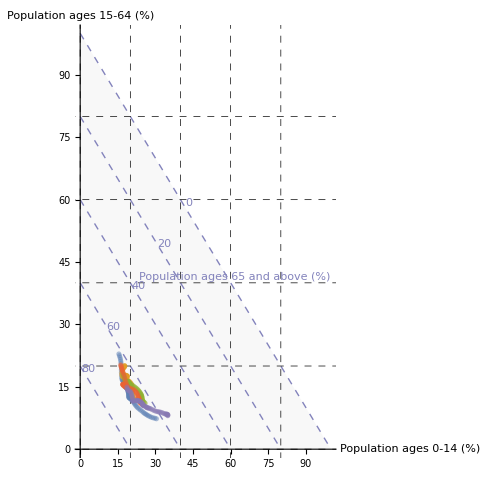

```mathematica
figFullTriangle=ListPlot[useSeries,
Prolog->{probTriangle,nonProbTriangle,
y2gridLines[20,y2color],
y2frameLabels[42,20,1.3,y2color],
y2frameTitle[y2Label,60,y2color]},
PlotStyle->(Opacity[.5,#]&/@countryColors),
PlotRange->{{0,100},{0,100}},PlotRangePadding->None,
GridLines->{Range[0,80,20]},GridLinesStyle->Directive[Black,Dashed],
AxesLabel->{xLabel,yLabel},
AspectRatio->1,
ImagePadding->Full,
ImageSize->500]
```

#### Customized SharesTriangle graphic: Handpick plot range and options

```mathematica
plotRange={{14,36},{5,25}};
frameStep=5;
xTicks=Range[15,35,frameStep];
yTicks=Range[5,25,frameStep];
y2Ticks=y2frameTicks[36,frameStep,y2color];
y2FrameCut=53;(* the x-coordinate above which y2 frame tick labels intersects the diagonal where y2=0. *)
y2FrameOffset=0.17; (* offset y2 frame tick labels towards north east *)
leaderSize=27; (* callout leader size *)
```

Label the first and last observation in each series

```mathematica
{firstLabels,lastLabels}=Table[Framed@StringJoin[#,"\n",ToString[year]]&/@countryLabels,{year,yearList[[{1,-1}]]}];
firstCallouts=MapThread[trianglePlotCallout[#1,#2,#3,leaderSize]&,{First/@useSeries,firstLabels,countryColors}];
lastCallouts=MapThread[trianglePlotCallout[#1,#2,#3,leaderSize]&,{Last/@useSeries,lastLabels,countryColors}];

figProbTriangle=Show[ListPlot[useSeries,
Prolog->{probTriangle,y2gridLines[frameStep,y2color],y2frameLabels[y2FrameCut,frameStep,y2FrameOffset,y2color]},
PlotStyle->(Opacity[.6,#]&/@countryColors),
PlotRange->plotRange,
GridLines->{xTicks,yTicks},GridLinesStyle->Directive[Lighter[Gray,.3],Dashed,Thickness[.0015]],
Frame->True,Axes->None,
FrameTicks->{{yTicks,y2Ticks},{xTicks,None}},
FrameLabel->{{yLabel,Style[Rotate[y2Label,180°],FontColor->y2color]},{xLabel,None}},
BaseStyle->Directive[FontSize->16],
LabelStyle->Directive[Black,FontSize->20]],
ListPlot[useSeries,
PlotStyle->(Opacity[.4,#]&/@countryColors),Joined->True],
ListPlot[{firstCallouts,lastCallouts}ᵀ,
PlotStyle->({PointSize->0.012,Opacity[.3,#]}&/@countryColors)],
ImageSize->1000,
ImagePadding->60,
AspectRatio->1]
```

-Graphics-

```mathematica
Export[FileNameJoin[{outputDir,"test.png"}],figProbTriangle,ImageSize->1600]
Export[FileNameJoin[{outputDir,"test.svg"}],figProbTriangle]
```

```mathematica
SystemOpen[%]
```